```mathematica
kB=Quantity["BoltzmannConstant"]
hbar=Quantity["ReducedPlanckConstant"]
Tc[m_, NoverV_]:= (2π  hbar^2)/(m  kB) * (NoverV / (Zeta[3/2]))^ (2/3)
```

k

ℏ

```mathematica
(* First, what's the number density of He^4? *)
```

```mathematica
HeNoverV=WolframAlpha["0.145g/cm^3  * (6.022e23/mol) / (molar mass of He4)","Result"]
```

2.18156×10^22 /cm^3

```mathematica
MHe4 = WolframAlpha["Mass of He4 in kg", "Result"]
```

6.64647907×10^-27 kg

```mathematica
Tc[MHe4, HeNoverV]
```

3.89113×10^41 ℏ^2/(kg cm^2 k)

```mathematica
UnitSimplify[Quantity[3.891126187438498*^41,("ReducedPlanckConstant")^2/("BoltzmannConstant" ("Centimeters")^2 "Kilograms")]]
```

3.13433 K

```mathematica
(*Number 3:*)
```

```mathematica
z[T_]:=If[T<1, 1, FindRoot[Zeta[5/2]/PolyLog[5/2, z] == T^(5/2), {z,  1/T^(5/2), 0, 1}][[1, 2]]]
```

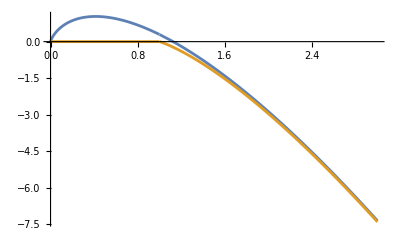

```mathematica
Plot[{T*Log[ClassicalZ[T]], T*Log[z[T]]}, {T, 0, 3}]
```

```mathematica
(*Classical limit for Z:*)
ClassicalZ[T_]:= Zeta[5/2] / (T)^(5/2)
```

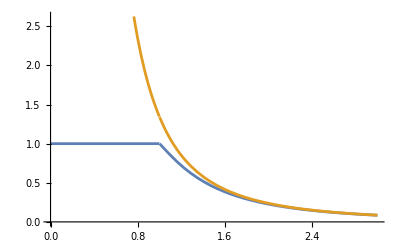

```mathematica
Plot[{z[T], ClassicalZ[T]}, {T, 0, 3}]
```

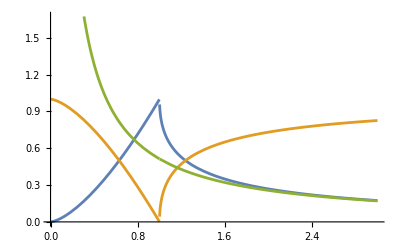

```mathematica
(* 3c: Worked with Bidisha on this*)
Ne[T_]:= If[T <1, T^(3/2), T^(3/2) *PolyLog[3/2, z[T]]/Zeta[3/2]]
No[T_]:= 1- Ne[T]
NeClass[T_] := Zeta[5/2]/Zeta[3/2] T^-1
Plot[{Ne[T], No[T], NeClass[T]}, {T, 0, 3}]
(*3d: Worked with Bidisha on this*)
DimLessEntrop[T_]:= If[T<1, T^(3/2),  ((5PolyLog[5/2, z[T]])/(2PolyLog[3/2, z[T]]) - Log[z[T]])/((5Zeta[5/2])/(2Zeta[3/2]))]
```

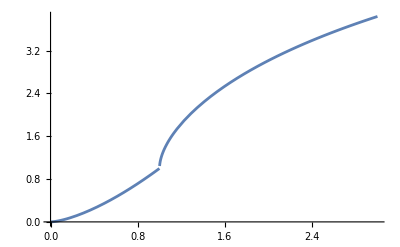

```mathematica
Plot[DimLessEntrop[T], {T, 0, 3}]
```

```mathematica
(* 3e: CoverNk: Worked with Bidisha on this*)
CoverNk[T_]:=If[T<1,15/4*Zeta[5/2]/Zeta[3/2]*T^(3/2),(25/4)*(PolyLog[1/2,z[T]]*(PolyLog[5/2,z[T]])^2/(PolyLog[3/2,z[T]])^3)-15/4*(PolyLog[5/2,z[T]]/(PolyLog[3/2,z[T]]))]
```

```mathematica
Function[T,If[T<1,(15 Zeta[5/2] T^(3/2))/(4 Zeta[3/2]),25/4 ((PolyLog[1/2,z[T]] PolyLog[5/2,z[T]]^2)/PolyLog[3/2,z[T]])^3-(15 PolyLog[5/2,z[T]])/(4 PolyLog[3/2,z[T]])]]
```

Function[T,If[T<1,(15 Zeta[5/2] T^(3/2))/(4 Zeta[3/2]),25/4 ((PolyLog[1/2,z[T]] PolyLog[5/2,z[T]]^2)/PolyLog[3/2,z[T]])^3-(15 PolyLog[5/2,z[T]])/(4 PolyLog[3/2,z[T]])]]

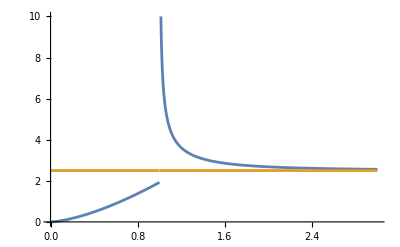

```mathematica
Plot[{CoverNk[T], 2.5},{T, 0, 3}, PlotRange -> {0, 10}]
```